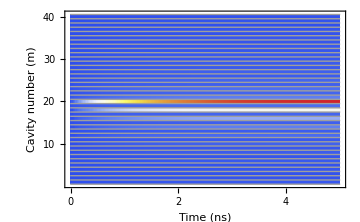

nonreciprocal_transport_1.pdf

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
texStyle={FontFamily->"Latin Modern Roman",FontSize->14,FontColor->Black};
SetOptions[ListPlot,BaseStyle->texStyle,Frame->True,Axes->False];
SetOptions[BarChart,BaseStyle->texStyle,Frame->True,Axes->False,FrameTicks->True];
SetOptions[ArrayPlot,BaseStyle->texStyle,Mesh->{All,None},Frame->True,PlotRangePadding->None,ColorFunction->"TemperatureMap",AspectRatio->1/GoldenRatio];
rhoRe=Import["org-pol-lat.h5",{"Data",3}];
ρ=Diagonal/@rhoRe;
ρ=Drop[ρ,1];
ρ=Transpose[ρ];
arrayplot=ArrayPlot[ρ,ImageSize->Medium,FrameLabel->{"Cavity number (m)","Time (ns)"},DataRange->{{0,5},{1,40}},FrameTicks->{True,True,False,False}]
Export["nonreciprocal_transport_1.pdf",arrayplot]
```